```mathematica
(*Riemman in optical metric*)
```

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)
```

```mathematica
DefManifold[M2,2,IndexRange[a,n]]
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]
```

```mathematica
DefChart[esfOp,M2,{1,2},{r[],Φ[]},ChartColor->Brown]
```

```mathematica
(*metric field*)
DefScalarFunction[hh,PrintAs->"h"]
DefScalarFunction[ff,PrintAs->"f"]
```

```mathematica
$Assumptions={r[]>0,Φ[]>0,Φ[]<2π};
MatrixForm[metricarray={{1/(ff[r[]]hh[r[]]),0},{0,r[]^2/hh[r[]]}}]
```

(1/(f[r] h[r]) | 0
0 | r^2/h[r])

```mathematica
metric2=CTensor[metricarray,{-esfOp,-esfOp}];
Invmetric2 =Inv[metric2];
```

```mathematica
(*CD=LC[metric]*)
cd=CovDOfMetric[metric2];
pd=PDOfBasis[esfOp];
```

```mathematica
Riemanncd=Riemann[cd];
```

```mathematica
rules={metric[a_?DownIndexQ,b_?DownIndexQ]:>metric2[a,b],
metric[a_?UpIndexQ,b_?UpIndexQ]:>Invmetric2[a,b],Det[g[]]->Det[metricarray],RiemannCD[a_?DownIndexQ,b_?DownIndexQ,c_?DownIndexQ,d_?DownIndexQ]:>Riemanncd[a,b,c,d]};
```

```mathematica
metric[a,b]/.rules
```

f[r] h[r] | 0
0 | h[r]/r^2 | a | b
  |

```mathematica
(* Vias 1*)
temp=RiemannCD[-a,-b,-c,-d]/Det[g[]];
temp2=temp//.rules;
Result=Head[temp2];
(*Result[[1, 3, 1, 3]]*)
```

```mathematica
(*total curvature K=R_{rϕrϕ}/dg*)
```

```mathematica
Kfunv0=-1/(√(metric2[{1,-esfOp},{1,-esfOp}]*metric2[{2,-esfOp},{2,-esfOp}]))((D[(1/(√metric2[{1,-esfOp},{1,-esfOp}])D[√metric2[{2,-esfOp},{2,-esfOp}],r[]]),r[]]+D[(1/(√metric2[{2,-esfOp},{2,-esfOp}])D[√metric2[{1,-esfOp},{1,-esfOp}],Φ[]]),Φ[]]))/.{r[]->r,Φ[]->Φ}//PowerExpand//Factor
```

(-2 h[r]^2 f'[r]+2 f[r] h[r] h'[r]+r h[r] f'[r] h'[r]-2 r f[r] h'[r]^2+2 r f[r] h[r] h''[r])/(4 r h[r])

```mathematica
Kfunv1 = (Riemann[cd][{1,-esfOp},{2,-esfOp},{1,-esfOp},{2,-esfOp}])/Det[g[]]/.rules/.{r[]->r,Φ[]->Φ}//Factor
```

(-2 h[r]^2 f'[r]+2 f[r] h[r] h'[r]+r h[r] f'[r] h'[r]-2 r f[r] h'[r]^2+2 r f[r] h[r] h''[r])/(4 r h[r])

```mathematica
Kfunv2=(RicciScalar[cd]/2/.rules)[[1]]/.{r[]->r,Φ[]->Φ}//Factor
```

(-2 h[r]^2 f'[r]+2 f[r] h[r] h'[r]+r h[r] f'[r] h'[r]-2 r f[r] h'[r]^2+2 r f[r] h[r] h''[r])/(4 r h[r])

```mathematica
Christoffel[cd,esfOp]
```

xAct`xTensor`Private`TensorPlus[Christoffel[PDesfOp,esfOp],CTensor[{{{-f'[r]/(2 f[r])-h'[r]/(2 h[r]),0},{0,(f[r] r (-2 h[r]+r h'[r]))/(2 h[r])}},{{0,1/r-h'[r]/(2 h[r])},{1/r-h'[r]/(2 h[r]),0}}},{esfOp,-esfOp,-esfOp},0]]

```mathematica
term1={{{-f'[r]/(2 f[r])-h'[r]/(2 h[r]),0},{0,(f[r] r (-2 h[r]+r h'[r]))/(2 h[r])}},{{0,1/r-h'[r]/(2 h[r])},{1/r-h'[r]/(2 h[r]),0}}}[[2,1,1]];
term={{{-f'[r]/(2 f[r])-h'[r]/(2 h[r]),0},{0,(f[r] r (-2 h[r]+r h'[r]))/(2 h[r])}},{{0,1/r-h'[r]/(2 h[r])},{1/r-h'[r]/(2 h[r]),0}}}[[2,1,2]];
```

```mathematica
Kfunv3=1/(√Det[g[]])(D[(√Det[g[]])/metric2[{1,-esfOp},{1,-esfOp}] term1/.rules,Φ[]]-D[(√Det[g[]])/metric2[{1,-esfOp},{1,-esfOp}] term/.rules,r[]])/.rules/.{r[]->r,Φ[]->Φ}//Factor
```

(-2 h[r]^2 f'[r]+2 f[r] h[r] h'[r]+r h[r] f'[r] h'[r]-2 r f[r] h'[r]^2+2 r f[r] h[r] h''[r])/(4 r h[r])

```mathematica
(*check*)
```

```mathematica
Kfunv3-Kfunv0//Simplify
```

0

```mathematica
(*Sch*)
```

```mathematica
Sch={hh->Function[r, ff[r]],ff->Function[r,1-2G M/r]}; (*ff->Function[r,1-2G M/(cc^2r)]}*)
Kott={hh->Function[r, ff[r]],ff->Function[r,1-2G M/r-Λ r^2/3]}; (*ff->Function[r,1-2G M/(cc^2r)-Λ r^2/3]*)
```

```mathematica
Kfunv3//.Sch//Simplify//Expand//Simplify
```

(G M (3 G M-2 r))/r^4

```mathematica
Kfunv3//.Kott//Simplify//Expand
```

(3 G^2 M^2)/r^4-(2 G M)/r^3-Λ/3+(2 G M Λ)/r

```mathematica
Collect[%,Λ, Simplify]
```

(G M (3 G M-2 r))/r^4+(-1/3+(2 G M)/r) Λ

```mathematica
√Det[g[]]/.rules/.{r[]->r,Φ[]->Φ}//.Kott//PowerExpand//Simplify
```

r/((1-(2 G M)/r-(r^2 Λ)/3)^(3/2))

```mathematica
Solve[D[r[ϕ],ϕ]+ff[r]r^2==r^4 ff[r]/(b^2 hh[r])//.Kott,D[r[ϕ],ϕ]]//PowerExpand//Simplify
```

{{r'[ϕ]→r (2 G M-r+r^3 (1/b^2+Λ/3))}}

```mathematica
(*angle*)
```

```mathematica
tan=Sqrt[ff[r]]r D[ϕ[r],r]//.Kott//PowerExpand//Simplify
```

r √(1-(2 G M)/r-(r^2 Λ)/3) ϕ'[r]

```mathematica
(*geodesicas*)
```

```mathematica
Eq1= D[u[ϕ],ϕ]^2+u[ϕ]^2(1-u[ϕ]);
DSolve[Eq1==0, u[ϕ],ϕ]
```

{{u[ϕ]→1+Tan[1/2 (-ϕ+C[1])]^2},{u[ϕ]→1+Tan[(ϕ+C[1])/2]^2}}

```mathematica
DSolve[{Eq1==c1+c2}, u[ϕ],ϕ]
```

```mathematica
$Assumptions=M>=0&&G>=0
```

M≥0&&G≥0

```mathematica
(*Analisis de la serie*)
```

```mathematica
√(1-(2 G M)/r[ϕ]-(r[ϕ]^2 Λ)/3) r[ϕ]/r'[ϕ]/.r->Function[ϕ,b/u[ϕ]]/.G->rs/(2M)/.Λ->rs λ/b^3/.rs->Rs*b//Simplify
```

-(u[ϕ] √(1-(Rs λ)/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]

```mathematica
eq=Last@Solve[((r'[ϕ])^2==r [ϕ](2 G M-r[ϕ]+r[ϕ]^3 (1/b^2+Λ/3))/.r->Function[ϕ,b/u[ϕ]]/.G->rs/(2M)/.Λ->rs λ/b^3/.rs->Rs*b/.u'[ϕ]^2->u2//Simplify//Expand),u2]/.Rule->Equal/.u2->u'[ϕ]^2//Expand
```

{u'[ϕ]^2==1+(Rs λ)/3-u[ϕ]^2+Rs u[ϕ]^3}

```mathematica
(*Λ̄=Λ̂/(Rs b^2)*)
```

```mathematica
eq1=eq[[1,1]]-eq[[1,2]]
```

-1-(Rs λ)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2

```mathematica
(* ϵ -> rs/b=Rs *)
```

```mathematica
rU=u->Function[ϕ, (u0[ϕ]+ϵ u1[ϕ]+ϵ^2 u2[ϕ]+ϵ^3 u3[ϕ]+ϵ^4 u4[ϕ])];
(*rS=Rs->0+ϵ Rs+ϵ^2 Rs+ϵ^3 Rs;*)
(*rS=Rs->0+ϵ Rs+ϵ^2 Rs+ϵ^3 Rs;*)
(*ΛS=Λ̄->0+ϵ Λ̄*)
```

```mathematica
test=Collect[eq1/.rU/.ϵ->Rs,Rs ,Simplify];(*/.ΛS/.rS,*)
```

```mathematica
test;
```

```mathematica
test0=Coefficient[test,Rs,0]
test1=Coefficient[test,Rs,1]
test2=Coefficient[test,Rs,2]
test3=Coefficient[test,Rs,3]
test4=Coefficient[test,Rs,4]
```

-1+u0[ϕ]^2+u0'[ϕ]^2

-λ/3-u0[ϕ]^3+2 u0[ϕ] u1[ϕ]+2 u0'[ϕ] u1'[ϕ]

-3 u0[ϕ]^2 u1[ϕ]+u1[ϕ]^2+2 u0[ϕ] u2[ϕ]+u1'[ϕ]^2+2 u0'[ϕ] u2'[ϕ]

-3 u0[ϕ]^2 u2[ϕ]+u0[ϕ] (-3 u1[ϕ]^2+2 u3[ϕ])+2 (u1[ϕ] u2[ϕ]+u1'[ϕ] u2'[ϕ]+u0'[ϕ] u3'[ϕ])

-u1[ϕ]^3+u2[ϕ]^2-3 u0[ϕ]^2 u3[ϕ]+u1[ϕ] (-6 u0[ϕ] u2[ϕ]+2 u3[ϕ])+2 u0[ϕ] u4[ϕ]+u2'[ϕ]^2+2 u1'[ϕ] u3'[ϕ]+2 u0'[ϕ] u4'[ϕ]

```mathematica
Sl0=Solve[test0==0,u0'[ϕ]]//Expand
Sl1=Last@Solve[test1==0,u1'[ϕ]]//Expand
Sl2=Last@Solve[test2==0,u2'[ϕ]]//Expand
Sl3=Last@Solve[test3==0,u3'[ϕ]]//Expand
Sl4=Last@Solve[test4==0,u4'[ϕ]]//Expand
```

{{u0'[ϕ]→-√(1-u0[ϕ]^2)},{u0'[ϕ]→√(1-u0[ϕ]^2)}}

{u1'[ϕ]→λ/(6 u0'[ϕ])+u0[ϕ]^3/(2 u0'[ϕ])-(u0[ϕ] u1[ϕ])/u0'[ϕ]}

{u2'[ϕ]→(3 u0[ϕ]^2 u1[ϕ])/(2 u0'[ϕ])-u1[ϕ]^2/(2 u0'[ϕ])-(u0[ϕ] u2[ϕ])/u0'[ϕ]-u1'[ϕ]^2/(2 u0'[ϕ])}

{u3'[ϕ]→(3 u0[ϕ] u1[ϕ]^2)/(2 u0'[ϕ])+(3 u0[ϕ]^2 u2[ϕ])/(2 u0'[ϕ])-(u1[ϕ] u2[ϕ])/u0'[ϕ]-(u0[ϕ] u3[ϕ])/u0'[ϕ]-(u1'[ϕ] u2'[ϕ])/u0'[ϕ]}

{u4'[ϕ]→u1[ϕ]^3/(2 u0'[ϕ])+(3 u0[ϕ] u1[ϕ] u2[ϕ])/u0'[ϕ]-u2[ϕ]^2/(2 u0'[ϕ])+(3 u0[ϕ]^2 u3[ϕ])/(2 u0'[ϕ])-(u1[ϕ] u3[ϕ])/u0'[ϕ]-(u0[ϕ] u4[ϕ])/u0'[ϕ]-u2'[ϕ]^2/(2 u0'[ϕ])-(u1'[ϕ] u3'[ϕ])/u0'[ϕ]}

```mathematica
(*orden cero*)
```

```mathematica
$Assumptions=ϕ>0&&ϕ<π;
```

```mathematica
s0=Last@DSolve[Sl0[[1]]/.Rule->Equal,u0[ϕ],ϕ]
c0=Last@Solve[D[s0,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1],Reals]
```

{u0[ϕ]→-Sin[ϕ-C[1]]}

{C[1]→ConditionalExpression[-π+δ-2 π C[2], C[2]∈ℤ]}

```mathematica
soF=u0->Function[ϕ,Evaluate[(s0/.c0/.C[2]->0)[[1,2]]]]
```

u0→Function[ϕ,-Sin[δ-ϕ]]

```mathematica
Sl1Eq=Sl1/.soF
```

{u1'[ϕ]→1/6 λ Sec[δ-ϕ]-1/2 Sin[δ-ϕ]^2 Tan[δ-ϕ]+Tan[δ-ϕ] u1[ϕ]}

```mathematica
s1=Last@DSolve[Sl1Eq/.Rule->Equal,u1[ϕ],ϕ]//FullSimplify
c0=Last@Solve[D[s1,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1],Reals]//Simplify
```

{u1[ϕ]→3/4+1/4 Cos[2 δ-2 ϕ]+C[1] Cos[δ-ϕ]-1/6 λ Sin[δ-ϕ]}

{C[1]→0}

```mathematica
s1F=u1->Function[ϕ,Evaluate[(s1/.c0)[[1,2]]//FullSimplify]]
```

u1→Function[ϕ,1/12 (9+3 Cos[2 δ-2 ϕ]-2 λ Sin[δ-ϕ])]

```mathematica
Sl2Eq=Sl2/.soF/.s1F//Simplify
```

{u2'[ϕ]→-1/576 Sec[δ-ϕ] (-63+8 λ^2+27 Cos[4 δ-4 ϕ]+324 Cos[2 δ-2 ϕ]-24 λ Sin[3 δ-3 ϕ]+72 λ Sin[δ-ϕ]-576 Sin[δ-ϕ] u2[ϕ])}

```mathematica
s2=Last@DSolve[Sl2Eq/.Rule->Equal,u2[ϕ],ϕ]//FullSimplify
c0=Last@Solve[D[s2,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1]]//FullSimplify
```

{u2[ϕ]→1/576 (96 λ+6 Cos[δ-ϕ] (-90 ϕ+96 C[1]+16 λ Cos[δ-ϕ]+9 Sin[2 δ-2 ϕ])+(-63+8 λ^2) Sin[δ-ϕ]+297 Sec[δ] Sin[ϕ])}

{C[1]→1/64 (30 π+60 δ-33 Tan[δ])}

```mathematica
s2F=u2->Function[ϕ,Evaluate[(s2/.c0)[[1,2]]//FullSimplify]]
```

u2→Function[ϕ,1/576 (48 λ (3+Cos[2 δ-2 ϕ])+270 (π+2 δ-2 ϕ) Cos[δ-ϕ]+27 Sin[3 δ-3 ϕ]+(-333+8 λ^2) Sin[δ-ϕ])]

```mathematica
Sl3Eq=Sl3/.soF/.s1F/.s2F//Simplify
```

{u3'[ϕ]→1/6912 Sec[δ-ϕ] (378 λ+16 λ^3-162 λ Cos[4 δ-4 ϕ]-810 π Cos[3 δ-3 ϕ]-1620 δ Cos[3 δ-3 ϕ]+1620 ϕ Cos[3 δ-3 ϕ]-1944 λ Cos[2 δ-2 ϕ]-2430 π Cos[δ-ϕ]-4860 δ Cos[δ-ϕ]+4860 ϕ Cos[δ-ϕ]-81 Sin[5 δ-5 ϕ]+837 Sin[3 δ-3 ϕ]-5994 Sin[δ-ϕ]+6912 Sin[δ-ϕ] u3[ϕ])}

```mathematica
s3=Last@DSolve[Sl3Eq/.Rule->Equal,u3[ϕ],ϕ]//TrigToExp//Simplify
c0=Last@Solve[D[s3,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1]]//FullSimplify
```

{u3[ϕ]→1/(6912 (1+ⅇ^(2 ⅈ δ)))ⅇ^(-4 ⅈ (δ+ϕ)) (-27 ⅇ^(8 ⅈ δ)-27 ⅇ^(10 ⅈ δ)+12150 ⅇ^(6 ⅈ δ+4 ⅈ ϕ)-27 ⅇ^(8 ⅈ ϕ)+12150 ⅇ^(4 ⅈ (δ+ϕ))-27 ⅇ^(2 ⅈ (δ+4 ϕ))+81 ⅈ ⅇ^(3 ⅈ δ+7 ⅈ ϕ) λ-81 ⅈ ⅇ^(ⅈ (7 δ+ϕ)) λ-81 ⅈ ⅇ^(ⅈ (9 δ+ϕ)) λ+81 ⅈ ⅇ^(ⅈ (δ+7 ϕ)) λ+162 ⅇ^(4 ⅈ δ+6 ⅈ ϕ) (5 ⅈ π+2 (8+5 ⅈ δ-5 ⅈ ϕ))+162 ⅇ^(2 ⅈ (δ+3 ϕ)) (5 ⅈ π+2 (8+5 ⅈ δ-5 ⅈ ϕ))+162 ⅇ^(2 ⅈ (3 δ+ϕ)) (-5 ⅈ π+2 (8-5 ⅈ δ+5 ⅈ ϕ))+162 ⅇ^(2 ⅈ (4 δ+ϕ)) (-5 ⅈ π+2 (8-5 ⅈ δ+5 ⅈ ϕ))-27 ⅇ^(3 ⅈ δ+5 ⅈ ϕ) (λ (-3 ⅈ+60 ϕ)-128 C[1])-27 ⅇ^(7 ⅈ δ+3 ⅈ ϕ) (λ (3 ⅈ+60 ϕ)-128 C[1])+ⅇ^(5 ⅈ δ+3 ⅈ ϕ) (16 ⅈ λ^3-27 λ (-77 ⅈ+60 ϕ)+3456 C[1])+ⅇ^(5 ⅈ (δ+ϕ)) (-16 ⅈ λ^3-27 λ (77 ⅈ+60 ϕ)+3456 C[1]))}

{C[1]→15/64 (π+2 δ) λ-1/432 λ (135+λ^2) Tan[δ]}

```mathematica
s3F=u3->Function[ϕ,Evaluate[(s3/.c0)[[1,2]]//ExpToTrig//FullSimplify//Simplify]]
```

$Aborted

```mathematica
Sl4Eq=Sl4/.soF/.s1F/.s2F/.s3F//Simplify
```

{u4'[ϕ]→1/331776 Sec[δ-ϕ] (8343-36450 π^2-145800 π δ-145800 δ^2+1512 λ^2-160 λ^4+145800 π ϕ+291600 δ ϕ-145800 ϕ^2+810 Cos[6 δ-6 ϕ]-61479 Cos[4 δ-4 ϕ]-648 λ^2 Cos[4 δ-4 ϕ]-25920 π λ Cos[3 δ-3 ϕ]-51840 δ λ Cos[3 δ-3 ϕ]+51840 λ ϕ Cos[3 δ-3 ϕ]-652698 Cos[2 δ-2 ϕ]-7776 λ^2 Cos[2 δ-2 ϕ]-77760 π λ Cos[δ-ϕ]-155520 δ λ Cos[δ-ϕ]+155520 λ ϕ Cos[δ-ϕ]-2592 λ Sin[5 δ-5 ϕ]-21870 π Sin[4 δ-4 ϕ]-43740 δ Sin[4 δ-4 ϕ]+43740 ϕ Sin[4 δ-4 ϕ]+26784 λ Sin[3 δ-3 ϕ]-116640 π Sin[2 δ-2 ϕ]-233280 δ Sin[2 δ-2 ϕ]+233280 ϕ Sin[2 δ-2 ϕ]-191808 λ Sin[δ-ϕ]+331776 Sin[δ-ϕ] u4[ϕ])}

```mathematica
s4=Last@DSolve[Sl4Eq/.Rule->Equal,u4[ϕ],ϕ]//TrigToExp//Simplify
c0=Last@Solve[D[s4,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1]]//FullSimplify
```

{u4[ϕ]→1/(663552 (1+ⅇ^(2 ⅈ δ)))ⅇ^(-5 ⅈ (δ+ϕ)) (405 ⅈ ⅇ^(10 ⅈ δ)+405 ⅈ ⅇ^(12 ⅈ δ)-405 ⅈ ⅇ^(10 ⅈ ϕ)-405 ⅈ ⅇ^(2 ⅈ (δ+5 ϕ))+777600 ⅇ^(7 ⅈ δ+5 ⅈ ϕ) λ+777600 ⅇ^(5 ⅈ (δ+ϕ)) λ-1728 ⅇ^(ⅈ (9 δ+ϕ)) λ-1728 ⅇ^(ⅈ (11 δ+ϕ)) λ-1728 ⅇ^(3 ⅈ (δ+3 ϕ)) λ-1728 ⅇ^(ⅈ (δ+9 ϕ)) λ+10368 ⅇ^(3 ⅈ δ+7 ⅈ ϕ) λ (5 ⅈ π+2 (8+5 ⅈ δ-5 ⅈ ϕ))+10368 ⅇ^(5 ⅈ δ+7 ⅈ ϕ) λ (5 ⅈ π+2 (8+5 ⅈ δ-5 ⅈ ϕ))+10368 ⅇ^(7 ⅈ δ+3 ⅈ ϕ) λ (-5 ⅈ π+2 (8-5 ⅈ δ+5 ⅈ ϕ))+10368 ⅇ^(3 ⅈ (3 δ+ϕ)) λ (-5 ⅈ π+2 (8-5 ⅈ δ+5 ⅈ ϕ))-162 ⅇ^(4 ⅈ (δ+2 ϕ)) (-522 ⅈ+135 π+270 δ-4 ⅈ λ^2-270 ϕ)-162 ⅇ^(2 ⅈ (δ+4 ϕ)) (-522 ⅈ+135 π+270 δ-4 ⅈ λ^2-270 ϕ)-162 ⅇ^(2 ⅈ (4 δ+ϕ)) (522 ⅈ+135 π+270 δ+4 ⅈ λ^2-270 ϕ)-162 ⅇ^(2 ⅈ (5 δ+ϕ)) (522 ⅈ+135 π+270 δ+4 ⅈ λ^2-270 ϕ)+ⅈ ⅇ^(6 ⅈ (δ+ϕ)) (-1112535+72900 π^2+291600 δ^2-16632 λ^2+320 λ^4+7290 π (3 ⅈ+40 δ-20 ϕ)+1010880 ⅈ ϕ+12960 ⅈ λ^2 ϕ+145800 ϕ^2-14580 δ (-3 ⅈ+20 ϕ)-331776 ⅈ C[1])-ⅈ ⅇ^(6 ⅈ δ+4 ⅈ ϕ) (-1112535+72900 π^2+291600 δ^2-16632 λ^2+320 λ^4+7290 π (-3 ⅈ+40 δ-20 ϕ)-1010880 ⅈ ϕ-12960 ⅈ λ^2 ϕ+145800 ϕ^2-14580 δ (3 ⅈ+20 ϕ)+331776 ⅈ C[1])+81 ⅇ^(4 ⅈ δ+6 ⅈ ϕ) (1049 ⅈ+8 ⅈ λ^2+δ (-540-3600 ⅈ ϕ)-12480 ϕ-160 λ^2 ϕ+1800 ⅈ ϕ^2-90 ⅈ π (-3 ⅈ+20 ϕ)+4096 C[1])+81 ⅇ^(4 ⅈ (2 δ+ϕ)) (-1049 ⅈ-8 ⅈ λ^2-12480 ϕ-160 λ^2 ϕ-1800 ⅈ ϕ^2+90 ⅈ π (3 ⅈ+20 ϕ)+180 ⅈ δ (3 ⅈ+20 ϕ)+4096 C[1]))}

{C[1]→(ⅇ^(ⅈ δ) (405 (π+2 δ) (651+8 λ^2) Cos[δ]+(-299376+18225 (π+2 δ)^2+80 λ^2 (-54+λ^2)) Sin[δ]))/(82944 (1+ⅇ^(2 ⅈ δ)))}

```mathematica
s4F=u4->Function[ϕ,Evaluate[(s4/.c0)[[1,2]]//ExpToTrig//FullSimplify//Simplify]]
```

u4→Function[ϕ,1/331776(-1728 λ Cos[4 δ-4 ϕ]+81 (4800 λ-270 (π+2 δ-2 ϕ) Cos[3 δ-3 ϕ]+2048 λ Cos[2 δ-2 ϕ]+6240 (π+2 δ) Cos[δ-ϕ]+80 ((π+2 δ) λ^2-2 (78+λ^2) ϕ) Cos[δ-ϕ]-5 Sin[5 δ-5 ϕ]+1044 Sin[3 δ-3 ϕ]+8 λ (λ Sin[3 δ-3 ϕ]+80 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ]))+(-513783-7992 λ^2+160 λ^4+36450 (π+2 δ-2 ϕ)^2) Sin[δ-ϕ])]

```mathematica
(*Solución FInal*)
```

```mathematica
uSerie= Collect[(u0[ϕ]+Rs u1[ϕ]+Rs^2 u2[ϕ]+Rs^3 u3[ϕ]+Rs^4 u4[ϕ])/.soF/.s1F/.s2F/.s3F/.s4F,Rs,FullSimplify]
```

-Sin[δ-ϕ]+1/12 Rs (9+3 Cos[2 δ-2 ϕ]-2 λ Sin[δ-ϕ])+1/576 Rs^2 (48 λ (3+Cos[2 δ-2 ϕ])+270 (π+2 δ-2 ϕ) Cos[δ-ϕ]+27 Sin[3 δ-3 ϕ]+(-333+8 λ^2) Sin[δ-ϕ])+(Rs^3 (-27 Cos[4 δ-4 ϕ]+81 (75+32 Cos[2 δ-2 ϕ]+λ (10 (π+2 δ-2 ϕ) Cos[δ-ϕ]+Sin[3 δ-3 ϕ])+10 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ])-λ (999+8 λ^2) Sin[δ-ϕ]))/3456+1/331776 Rs^4 (-1728 λ Cos[4 δ-4 ϕ]+81 (4800 λ-270 (π+2 δ-2 ϕ) Cos[3 δ-3 ϕ]+2048 λ Cos[2 δ-2 ϕ]+6240 (π+2 δ) Cos[δ-ϕ]+80 ((π+2 δ) λ^2-2 (78+λ^2) ϕ) Cos[δ-ϕ]-5 Sin[5 δ-5 ϕ]+1044 Sin[3 δ-3 ϕ]+8 λ (λ Sin[3 δ-3 ϕ]+80 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ]))+(-513783-7992 λ^2+160 λ^4+36450 (π+2 δ-2 ϕ)^2) Sin[δ-ϕ])

```mathematica
eqPaper=Collect[uSerie/.λ ->Λ̄/Rs//Simplify,{Rs,λ },FullSimplify]
```

1/12 Rs (3+Cos[2 δ-2 ϕ]) (3+Λ̄)+1/384 Rs^3 (3+2 Λ̄) (225-Cos[4 δ-4 ϕ]+96 Cos[2 δ-2 ϕ]+30 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ])+(Rs^2 (24+Λ̄ (12+Λ̄)) (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ]))/1536+((-10368+Λ̄ (-1728+Λ̄ (144+Λ̄ (-24+5 Λ̄)))) Sin[δ-ϕ])/10368+(Rs^4 (-15 (π+2 δ-2 ϕ) (9 Cos[3 δ-3 ϕ]-208 Cos[δ-ϕ])+(3 (-884+75 (π+2 δ-2 ϕ)^2)-5 Cos[4 δ-4 ϕ]+1039 Cos[2 δ-2 ϕ]) Sin[δ-ϕ]))/2048

```mathematica
ord0=Coefficient[eqPaper,Rs,0]
ord1=Coefficient[eqPaper,Rs,1]
ord2=Coefficient[eqPaper,Rs,2]
ord3=Coefficient[eqPaper,Rs,3]
```

((-10368+Λ̄ (-1728+Λ̄ (144+Λ̄ (-24+5 Λ̄)))) Sin[δ-ϕ])/10368

1/12 (3+Cos[2 δ-2 ϕ]) (3+Λ̄)

((24+Λ̄ (12+Λ̄)) (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ]))/1536

1/384 (3+2 Λ̄) (225-Cos[4 δ-4 ϕ]+96 Cos[2 δ-2 ϕ]+30 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ])

```mathematica
Collect[ord0,Λ̄]
Collect[ord1,Λ̄]
Collect[ord2,Λ̄]
```

-Sin[δ-ϕ]-1/6 Λ̄ Sin[δ-ϕ]+1/72 (Λ̄)^2 Sin[δ-ϕ]-1/432 (Λ̄)^3 Sin[δ-ϕ]+(5 (Λ̄)^4 Sin[δ-ϕ])/10368

1/4 (3+Cos[2 δ-2 ϕ])+1/12 (3+Cos[2 δ-2 ϕ]) Λ̄

1/64 (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ])+1/128 Λ̄ (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ])+((Λ̄)^2 (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ]))/1536

```mathematica
(*De Sitter*)
```

```mathematica
dS=eqPaper/.Rs->0//Expand
```

-Sin[δ-ϕ]-1/6 Λ̄ Sin[δ-ϕ]+1/72 (Λ̄)^2 Sin[δ-ϕ]-1/432 (Λ̄)^3 Sin[δ-ϕ]+(5 (Λ̄)^4 Sin[δ-ϕ])/10368

```mathematica
dS/.δ->0
```

Sin[ϕ]+1/6 Λ̄ Sin[ϕ]-1/72 (Λ̄)^2 Sin[ϕ]+1/432 (Λ̄)^3 Sin[ϕ]-(5 (Λ̄)^4 Sin[ϕ])/10368

```mathematica
(*checking that recovery Sch, Λ=0, δ->0*)
(*comparar con paper
https://arxiv.org/pdf/1110.6735.pdf
10.1103@PhysRevD.101.104032

Upaper =u_nuestro/b
*)
```

```mathematica
Collect[Sin[ϕ]+1/6 Rs (3+3 Cos[ϕ]^2+Λ̄ Sin[ϕ])/.Rs->{1+ϵ Rs},ϵ,TrigExpand]
```

{3/4+Cos[ϕ]^2/4+Sin[ϕ]+1/6 Λ̄ Sin[ϕ]-Sin[ϕ]^2/4+ϵ ((3 Rs)/4+1/4 Rs Cos[ϕ]^2+1/6 Rs Λ̄ Sin[ϕ]-1/4 Rs Sin[ϕ]^2)}

```mathematica
uSerie/.δ->0//FullSimplify
```

Sin[ϕ]+1/6 Rs (3+3 Cos[ϕ]^2+Λ̄ Sin[ϕ])+1/576 Rs^2 (48 (3+Cos[2 ϕ]) Λ̄-8 (Λ̄)^2 Sin[ϕ]+9 (30 (π-2 ϕ) Cos[ϕ]+37 Sin[ϕ]-3 Sin[3 ϕ]))+1/3456 Rs^3 (Λ̄ (999+8 (Λ̄)^2) Sin[ϕ]+27 (225+96 Cos[2 ϕ]-Cos[4 ϕ]+30 (π-2 ϕ) Cos[ϕ] (Λ̄-2 Sin[ϕ])-3 Λ̄ Sin[3 ϕ]))

```mathematica
ruleSch={Λ̄->0,δ->0};
```

```mathematica
Collect[eqPaper/.ruleSch//FullSimplify,Rs,Simplify]
```

1/4 Rs (3+Cos[2 ϕ])+Sin[ϕ]+(Rs^4 (15 (π-2 ϕ) (208 Cos[ϕ]-9 Cos[3 ϕ])+(2652-225 (π-2 ϕ)^2-1039 Cos[2 ϕ]+5 Cos[4 ϕ]) Sin[ϕ]))/2048+1/128 Rs^3 (225+96 Cos[2 ϕ]-Cos[4 ϕ]-30 (π-2 ϕ) Sin[2 ϕ])+1/64 Rs^2 (30 (π-2 ϕ) Cos[ϕ]+37 Sin[ϕ]-3 Sin[3 ϕ])

```mathematica
(*Comparando con Λ
10.1103@PhysRevD.101.104032, notar que es primer orden
*)
```

```mathematica
1/576 (48 (3+Cos[2 δ-2 ϕ]) Λ̄+27 (10 (π+2 δ-2 ϕ) Cos[δ-ϕ]+Sin[3 δ-3 ϕ])+(-333+8 (Λ̄)^2) Sin[δ-ϕ])/.Λ̄ ->Λ b^2/.δ->0//Expand
```

(b^2 Λ)/4+15/32 π Cos[ϕ]-15/16 ϕ Cos[ϕ]+1/12 b^2 Λ Cos[2 ϕ]+(37 Sin[ϕ])/64-1/72 b^4 Λ^2 Sin[ϕ]-3/64 Sin[3 ϕ]

```mathematica
(*ecuación de Flavio*)
```

```mathematica
ϵ^2 ((15 π μ^2 Cos[ϕ])/(32 b^3)+Cos[ϕ] (-(15 μ^2 ϕ)/(16 b^3)-(3 μ^2 Sin[2 ϕ])/(32 b^3)+1/6 b Λ Tan[ϕ]+(5 μ^2 Tan[ϕ])/(8 b^3)))//FullSimplify//TrigExpand//Expand
```

(15 π ϵ^2 μ^2 Cos[ϕ])/(32 b^3)-(15 ϵ^2 μ^2 ϕ Cos[ϕ])/(16 b^3)+1/6 b ϵ^2 Λ Sin[ϕ]+(37 ϵ^2 μ^2 Sin[ϕ])/(64 b^3)-(9 ϵ^2 μ^2 Cos[ϕ]^2 Sin[ϕ])/(64 b^3)+(3 ϵ^2 μ^2 Sin[ϕ]^3)/(64 b^3)

```mathematica
(**)
```

```mathematica
ClearAll[u]
```

```mathematica
Quit[]
```

```mathematica
(*
Test probando en una región donde sabemos que es válida nuestra aproximación
*)
```

```mathematica
Λf = 1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
M=1Msun;
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
b =2.8RSch;(*m*)
Rsval=RSch/b;(*Rs=rs/b*)
Lval=Λf*b^2; (*Λ̄ = Λ b^2 -> *)
ϕMin=0.4;
ϕMax=π-0.4;
δval=0;
```

```mathematica
uSeriePaper=-Sin[δ-ϕ](1+(Λ̄)/6-(Λ̄ ^2)/72)+(3+Cos[2ϕ-2δ])/4(1+(Λ̄)/3)Rs+((37Sin[ϕ-δ]-3Sin[3ϕ-3δ]+30(π-2(ϕ-δ))Cos[ϕ-δ])/64)(1+(Λ̄)/2+(Λ̄ ^2)/24)Rs^2;

uSerieT=1/12 Rs (3+Cos[2 δ-2 ϕ]) (3+Λ̄)+1/384 Rs^3 (3+2 Λ̄) (225-Cos[4 δ-4 ϕ]+96 Cos[2 δ-2 ϕ]+30 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ])+(Rs^2 (24+Λ̄ (12+Λ̄)) (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ]))/1536+((-10368+Λ̄ (-1728+Λ̄ (144+Λ̄ (-24+5 Λ̄)))) Sin[δ-ϕ])/10368+(Rs^4 (-15 (π+2 δ-2 ϕ) (9 Cos[3 δ-3 ϕ]-208 Cos[δ-ϕ])+(3 (-884+75 (π+2 δ-2 ϕ)^2)-5 Cos[4 δ-4 ϕ]+1039 Cos[2 δ-2 ϕ]) Sin[δ-ϕ]))/2048;(*serie Full*)

uSerie3=(Rs Cos[ϕ] (Cos[ϕ]+Sec[ϕ]))/2+Sin[ϕ]+((15 π Rs^2 Cos[ϕ])/32+Cos[ϕ] (-(15 Rs^2 ϕ)/16-(3 Rs^2 Sin[2 ϕ])/32+1/6 Λ̄ Tan[ϕ]+(5 Rs^2 Tan[ϕ])/8));
SerieRef=Function[ϕ,Evaluate[Sin[δ-ϕ]+Rs/2(1+Cos[δ-ϕ]^2)+(Λ̄)/6 Sin[δ-ϕ]+(Rs Λ̄)/6(1+Cos[δ-ϕ]^2)/.{Λ̄->Lval,Rs->Rsval}/.δ->δval]];
```

```mathematica
(*Método *)
```

```mathematica
perfT=Function[ϕ,Evaluate[uSerieT/.{Λ̄->Lval,Rs->Rsval}/.δ->δval]];
perfP=Function[ϕ,Evaluate[uSeriePaper/.{Λ̄->Lval,Rs->Rsval}/.δ->δval]];
```

```mathematica
perfP[ϕMin]
```

0.871576

```mathematica
sol0=NDSolve[{-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMin]==perfP[ϕMin]}/.{Λ̄->Lval,Rs->Rsval},{u,u'},{ϕ,ϕMin,ϕMax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->30]
```

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

```mathematica
sol1=NDSolve[{-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u'[π/2+δval]==0.00005}/.{Λ̄->Lval,Rs->Rsval},{u,u'},{ϕ,ϕMin,ϕMax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]
```

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

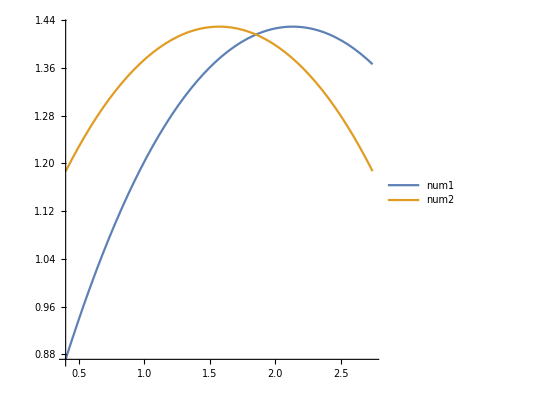

```mathematica
p1=Plot[{u[ϕ]/.sol0[[1]],u[ϕ]/.sol1[[1]]},{ϕ,ϕMin,ϕMax},AspectRatio->1,PlotLegends->{"num1","num2","perfT","perfP"},PlotRange->All]
```

```mathematica
perfT[ϕ],perfP[ϕ]
```

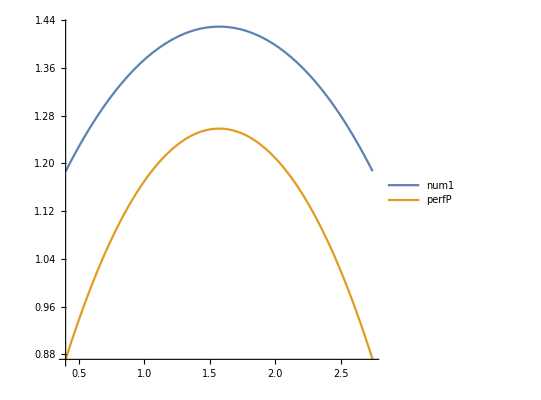

```mathematica
p1=Plot[{u[ϕ]/.sol1[[1]],perfP[ϕ]},{ϕ,ϕMin,ϕMax},AspectRatio->1,PlotLegends->{"num1","perfP"}]
```

#### Triangulos

```mathematica
Quit[]
```

```mathematica
a=1.5;
```

```mathematica
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
Λf =1.1056 10^-52;(*1.1056 10^-52 m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
(*C1*)
b0 =5*RSch;(*m*)(*5*RSch Rsun/RSch*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

sol1=NDSolve[{-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]

sol1F=NDSolve[({-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]
```

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

```mathematica
(*C2*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;
(*δval=0;*)
sol2=NDSolve[{-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMin2]==(u[ϕMin2]/.sol1[[1]])*b1/b0}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]
sol2F=NDSolve[({-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMin2]==(u[ϕMin2]/.sol1F[[1]])*b1/b0}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]
```

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

```mathematica
(*C3*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;
(*δval=0;*)
sol3=NDSolve[{-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMax3]==(u[ϕMax3]/.sol1[[1]])*b2/b0}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]

sol3F=NDSolve[({-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMax3]==(u[ϕMax3]/.sol1F[[1]])*b2/b0}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40](*,Method->{"EquationSimplification"->"Residual"},PrecisionGoal->20*)
```

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

```mathematica
Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,ϕMax1}, PlotRange->{{-1.5, 1.5},{0.5,1.9}},AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->{{-1.5, 1.5},{0.5,1.9}},PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->{{-1.5, 1.5},{0.5,1.9}},PlotStyle->Gray,AspectRatio->1];
```

```mathematica
Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,ϕMax1}, PlotStyle->Dashed,PlotRange->{{-1.5, 1.5},{0.5,1.9}},AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->{{-1.5, 1.5},{0.5,1.9}},PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->{{-1.5, 1.5},{0.5,1.9}},PlotStyle->{Dashed,Gray},AspectRatio->1];
```

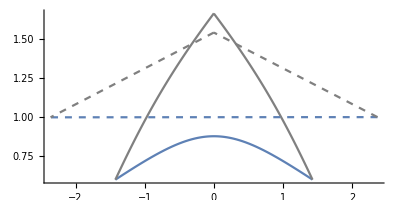

```mathematica
Show[{Pc1,Pc2, Pc3,Pc1F,Pc2F,Pc3F},PlotRange->All]
```

```mathematica
Pc12=Plot[u[ϕ]/.sol1[[1]],{ϕ,ϕMin1,ϕMax1},AspectRatio->0.5];
Pc22=Plot[b0/b1*u[ϕ]/.sol2[[1]],{ϕ,ϕMin2,ϕMax2},PlotStyle->Gray,AspectRatio->1];
Pc32=Plot[b0/b2*u[ϕ]/.sol3[[1]],{ϕ,ϕMin3,ϕMax3},PlotStyle->Gray,AspectRatio->1];
```

```mathematica
Pc1F2=Plot[u[ϕ]/.sol1F[[1]],{ϕ,ϕMin1,ϕMax1}, PlotStyle->Dashed,AspectRatio->0.5];
Pc2F2=Plot[b0/b1*u[ϕ]/.sol2F[[1]],{ϕ,ϕMin2,ϕMax2},PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F2=Plot[b0/b1*u[ϕ]/.sol3F[[1]],{ϕ,ϕMin3,ϕMax3},PlotStyle->{Dashed,Gray},AspectRatio->1];
```

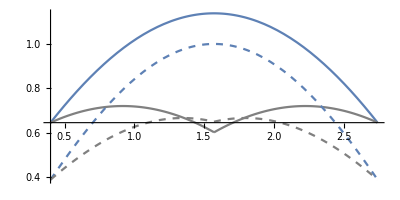

```mathematica
Show[{Pc12,Pc22, Pc32,Pc1F2,Pc2F2,Pc3F2},PlotRange->All]
```

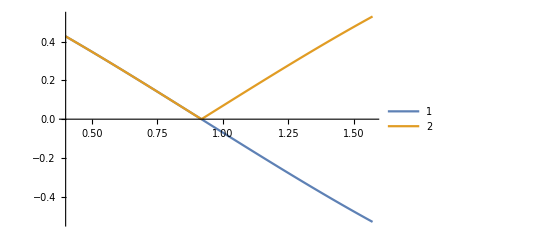

```mathematica
Plot[{u'[ϕ]/.sol2,Sqrt[1+(Λ̄)/3-u[ϕ]^2+Rs u[ϕ]^3]/.{Λ̄->Lval2,Rs->Rsval2}/.sol2},{ϕ,ϕMin2,ϕMax2},PlotLegends->Automatic]
```

```mathematica
(*Angulos*)
```

```mathematica
ptos={ϕMax1,π/2,ϕMin1};
Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]];
```

```mathematica
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1],Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1],Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];

betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
Total[betas-betasF]
```

-0.133396

```mathematica
angC1F
angC2F
angC3F
```

{0.400361,-0.385495}

{-0.623498,1.33177}

{-1.34638,0.605301}

```mathematica
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ]));
```

```mathematica
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delt=π/2-ϕ/.delI
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{0.652846}

```mathematica
angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c]
```

{-0.123429}

```mathematica
Quit[]
```

```mathematica
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ]));
```

```mathematica
Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]];
```

```mathematica
Λf =1.1056 10^-52;(*1.1056 10^-52 m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
a=1.5;
```

```mathematica
b0val={5,5.5,6,7,8,9,10,11,12,13,14,15,20,25,30,40,50,60,80,100,150,200,300,500,1000,5000,10000,20000,40000,80000,100000,150000,200000,235672,250000};
```

```mathematica
ptos={ϕMax1,π/2,ϕMin1};
```

```mathematica
DatAngN={};
DatAngSe={};
Do[
b=b0val[[i]];

(*C1*)
b0 =b*RSch;(*m*)(*5*RSch Rsun/RSch*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

sol1=NDSolve[{-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];

sol1F=NDSolve[({-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];

(*C2*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;
sol2=NDSolve[{-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMin2]==(u[ϕMin2]/.sol1[[1]])*b1/b0}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];
sol2F=NDSolve[({-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMin2]==(u[ϕMin2]/.sol1F[[1]])*b1/b0}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*C3*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;
sol3=NDSolve[{-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMax3]==(u[ϕMax3]/.sol1[[1]])*b2/b0}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];
sol3F=NDSolve[({-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0,u[ϕMax3]==(u[ϕMax3]/.sol1F[[1]])*b2/b0}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,ϕMax1}, PlotRange->{{-1.5, 1.5},{0.5,1.9}},AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->{{-1.5, 1.5},{0.5,1.9}},PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->{{-1.5, 1.5},{0.5,1.9}},PlotStyle->Gray,AspectRatio->1];
Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,ϕMax1}, PlotStyle->Dashed,PlotRange->{{-1.5, 1.5},{0.5,1.9}},AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->{{-1.5, 1.5},{0.5,1.9}},PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->{{-1.5, 1.5},{0.5,1.9}},PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc2, Pc3,Pc1F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)

(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1],Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1],Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];

(*Salvando*)
AppendTo[DatAngN,{b,Abs@Total[betas-betasF]}];
AppendTo[DatAngSe,{b,Abs@ASer}],
{i, 1, Length[b0val]}
]
```

```mathematica
Export["dataAngMathe.dat", DatAngN]
Export["dataAngSerMathe.dat", DatAngSe]
```

dataAngMathe.dat

dataAngSerMathe.dat

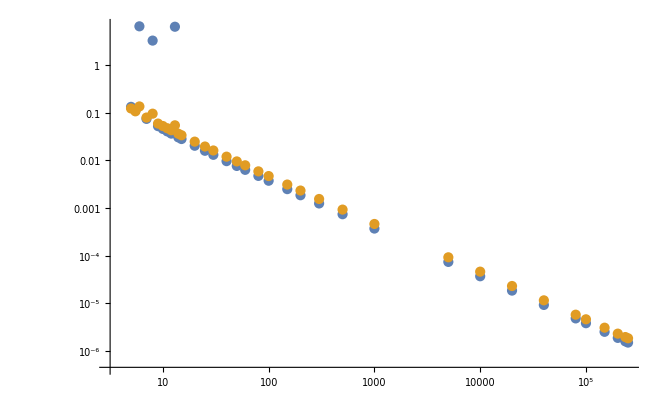

```mathematica
ListLogLogPlot[{DatAngN,DatAngSe}]
```